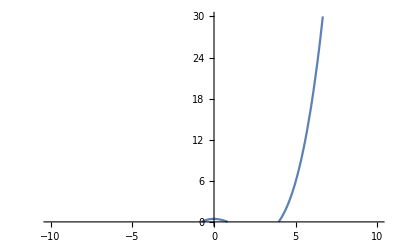

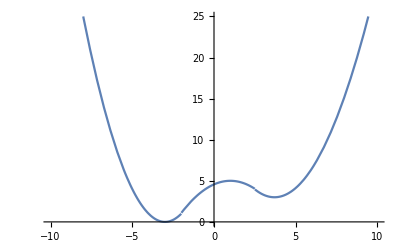

```mathematica
f[x_]:=If[x<-2, (x+3)^2,0]+If[x>=-2&&x<2.5,-(x-1)^2/2.3+5,0]+If[x>=2.5,(x-3.7)^2/1.5+3,0];
Plot[f[x], {x, -10, 10}, PlotRange->{{-10, 10}, {0, 25}}]
```

```mathematica
xdata = Table[f[i], {i, -10, 10, 1}]
```

{49,36,25,16,9,4,1,0,1.08696,3.26087,4.56522,5.,4.56522,3.32667,3.06,4.12667,6.52667,10.26,15.3267,21.7267,29.46}

```mathematica
ydata = Subdivide[-9, 9, 20]
```

{-9,-81/10,-36/5,-63/10,-27/5,-9/2,-18/5,-27/10,-9/5,-9/10,0,9/10,9/5,27/10,18/5,9/2,27/5,63/10,36/5,81/10,9}

```mathematica
Transpose[{xdata, ydata}]
```

{{49,-9},{36,-81/10},{25,-36/5},{16,-63/10},{9,-27/5},{4,-9/2},{1,-18/5},{0,-27/10},{1.08696,-9/5},{3.26087,-9/10},{4.56522,0},{5.,9/10},{4.56522,9/5},{3.32667,27/10},{3.06,18/5},{4.12667,9/2},{6.52667,27/5},{10.26,63/10},{15.3267,36/5},{21.7267,81/10},{29.46,9}}

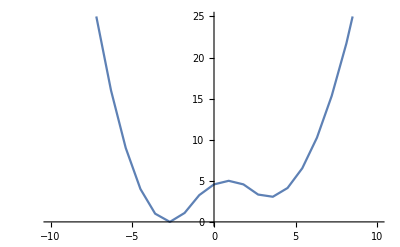

```mathematica
ListLinePlot[Transpose[{ydata, xdata}],PlotRange->{{-10, 10}, {0, 25}}]
```

```mathematica
fit = FindFit[Transpose[{ydata, xdata}], a+b*x+c*x^2+d*x^3+e*x^4+g*x^5+h*x^6+k*x^7+l*x^8+m*x^9, {a, b, c, d, e,g,h,k,l,m}, x]
```

{a→4.35346,b→1.14837,c→-0.532168,d→-0.0850787,e→0.0325757,g→0.00184425,h→-0.000421523,k→-0.0000221163,l→2.05175×10^-6,m→1.00158×10^-7}

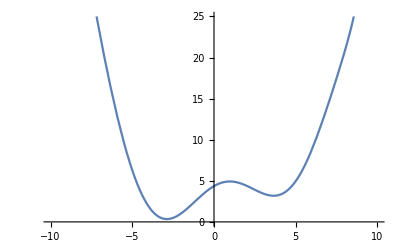

```mathematica
Plot[a+b*x+c*x^2+d*x^3+e*x^4+g*x^5+h*x^6+k*x^7+l*x^8+m*x^9/.fit, {x, -10, 10},PlotRange->{{-10, 10}, {0, 25}}]
```